```mathematica
ClearAll["Global`*"]
```

```mathematica
?x
```

Global`x

```mathematica
(*1b, 2b*)
```

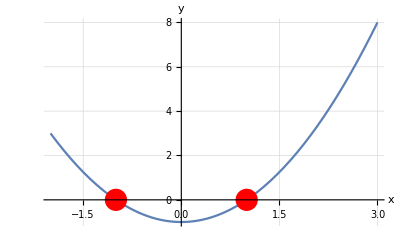

```mathematica
Plot[x^2 -1, {x,-2,3}, AxesLabel -> {"x","y"}, LabelStyle ->(FontSize->16),GridLines -> Automatic, Epilog ->{
(* graphics drawn after the plot *)
Red,PointSize[0.04],Point[{x1,0}],Point[{x2,0}]}]
{x1,x2} = x/.Solve[x^2-1 == 0,x];
x1
```

```mathematica
-1
ClearAll["Global`*"]
```

-1

```mathematica
(* Övning 3*)
sol = Solve[Sin[x] = 0,x]
x/.sol/.Table[{C[1]->i},{i,10}]//Simplify
```

Set::write: Tag Sin in Sin[x] is Protected.

Solve::naqs: 0 is not a quantified system of equations and inequalities.

Solve[0,x]

ReplaceAll::reps: {Solve[0, x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{x/.Solve[0,x],x/.Solve[0,x],x/.Solve[0,x],x/.Solve[0,x],x/.Solve[0,x],x/.Solve[0,x],x/.Solve[0,x],x/.Solve[0,x],x/.Solve[0,x],x/.Solve[0,x]}

```mathematica
(* Övning 4b*)
a=2;
D[Sin[a x],x]
```

2 Cos[2 x]

```mathematica
(* Övning 5*)
ClearAll["Global`*"]
```

```mathematica
f[x_]:=0.1

(*Övning 6*)
ClearAll["Global`*"]
?Integrate
Integrate[0.1x^3-7x+1,x]
```

RowBox[{"Integrate", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"]}], "]"}] gives the indefinite integral RowBox[{"∫", StyleBox["f", "TI"], " ", StyleBox["d", "TI"], StyleBox["x", "TI"]}]. 
RowBox[{"Integrate", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] gives the definite integral RowBox[{SubsuperscriptBox["∫", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]], " ", StyleBox["f", "TI"], " ", StyleBox["d", "TI"], StyleBox["x", "TI"]}]. 
RowBox[{"Integrate", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] gives the multiple integral RowBox[{SubsuperscriptBox["∫", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]], RowBox[{StyleBox["d", "TI"], StyleBox["x", "TI"], RowBox[{SubsuperscriptBox["∫", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]], RowBox[{StyleBox["d", "TI"], "", StyleBox["y", "TI"], " ", "…", " ", StyleBox["f", "TI"]}]}]}]}]. 
RowBox[{"Integrate", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] integrates over the geometric region StyleBox["reg", "TI"].

```mathematica
x-(7 x^2)/2+0.025 x^4
```